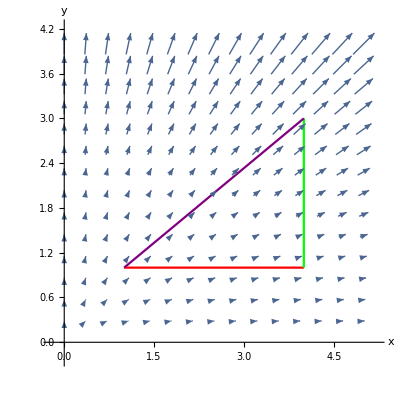

```mathematica
Show[VectorPlot[{x*y,y^2},{x,0,5},{y,0,4},AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"}],ParametricPlot[{x,1},{x,1,4},PlotStyle->Red],ParametricPlot[{4,y},{y,1,3},PlotStyle->Green],ParametricPlot[{1,1}+t*{3,2},{t,0,1},PlotStyle->Purple],AspectRatio->1]
```

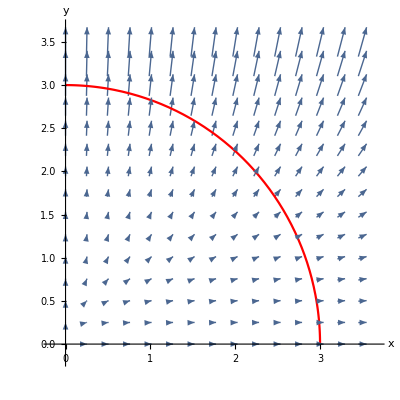

```mathematica
Show[VectorPlot[{x,y^2},{x,0,3.5},{y,0,3.5},AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"}],ParametricPlot[{3Cos[x],3Sin[x]},{x,0,π/2},PlotStyle->Red],AspectRatio->1]
```

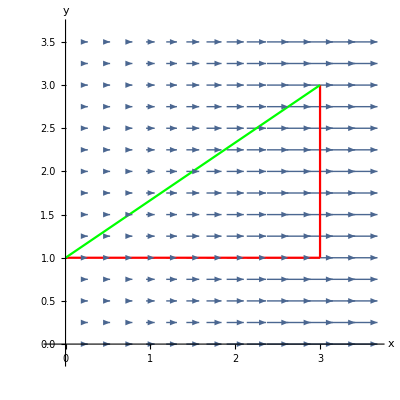

```mathematica
Show[VectorPlot[{x,0},{x,0,3.5},{y,0,3.5},AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"}],ParametricPlot[{x,1},{x,0,3},PlotStyle->Red],ParametricPlot[{3,y},{y,1,3},PlotStyle->Red],ParametricPlot[{0,1}+t{3,2},{t,0,1},PlotStyle->Green],AspectRatio->1]
```

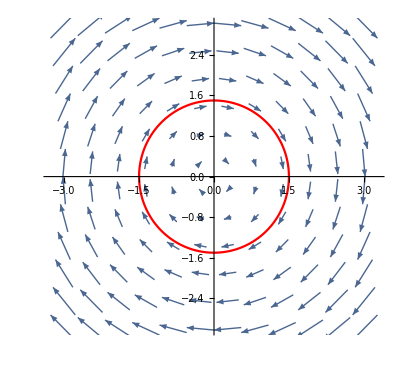

```mathematica
Show[ParametricPlot[{1.5Cos[t],1.5Sin[t]},{t,0,2π},PlotStyle->Red],
VectorPlot[{y,-x},{x,-3,3},{y,-3,3},AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"},VectorPoints->12],PlotRange->{-3,3}]
```

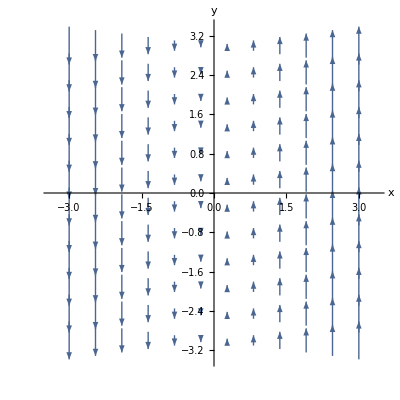

```mathematica
VectorPlot[{0,x},{x,-3,3},{y,-3,3},AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"},VectorPoints->12]
```

```mathematica
VectorPlot3D[-Quantity["GravitationalConstant"]*1*5.972*10^24*{x,y,z}/√(x^2+y^2+z^2)^3,{x,-1,1},{y,-1,1},{z,-1,1},VectorScale->0.2,VectorStyle->"Arrow3D",VectorPoints->6,Axes->True,Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
?Boxed
```

Boxed is an option for Graphics3D that specifies whether to draw the edges of the bounding box in a three-dimensional picture.

```mathematica
?ContourPlot
```

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a contour plot of f as a function of x and y. 
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}] plots contour lines for which f=g. 
ContourPlot[{f_1==g_1,f_2==g_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several contour lines. 
ContourPlot[…,{x,y}∈reg] takes the variables {x,y} to be in the geometric region reg.

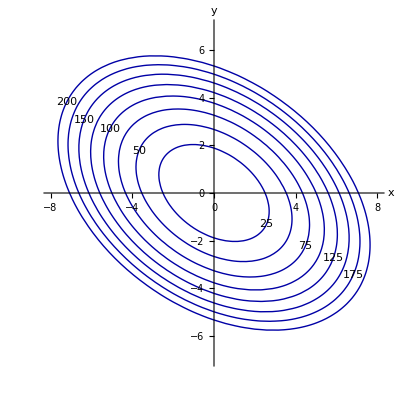

```mathematica
ContourPlot[4x^2 +4x*y+7y^2,{x,-8,8},{y,-7,7},ContourShading->None,ContourLabels->True,AxesOrigin->{0,0},Axes->True,Frame->False,Contours->{25,50,75,100,125,150,175,200},AxesLabel->{"x","y"},ContourStyle->Darker[Blue,0.35],BaseStyle->FontSize->14]
```

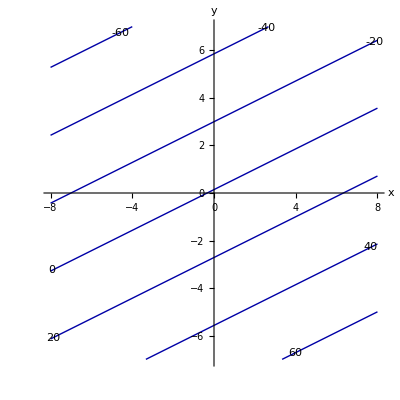

```mathematica
ContourPlot[3x-7y+1,{x,-8,8},{y,-7,7},ContourShading->None,ContourLabels->True,AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"},ContourStyle->Darker[Blue,0.35],BaseStyle->FontSize->14]
```

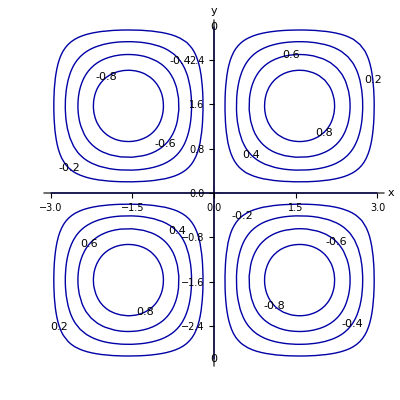

```mathematica
ContourPlot[Sin[x]*Sin[y],{x,-3,3},{y,-3,3},ContourShading->None,ContourLabels->True,AxesOrigin->{0,0},Axes->True,Frame->False,AxesLabel->{"x","y"},ContourStyle->Darker[Blue,0.35],BaseStyle->FontSize->14]
```